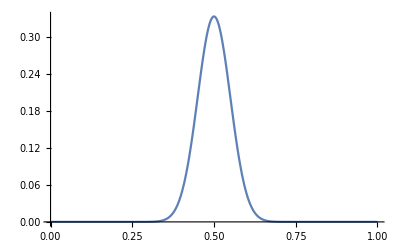

```mathematica
q[t_,x_]:=1/3*E^(-200(x-t-1/2)^2)
Plot[q[0,x],{x,0,1},PlotRange->All]
```

```mathematica
D[q[t,x],t]+D[q[t,x]^2-q[t,x]^3,x]
```

400/9 ⅇ^(-600 (-1/2-t+x)^2) (-1/2-t+x)-800/9 ⅇ^(-400 (-1/2-t+x)^2) (-1/2-t+x)+400/3 ⅇ^(-200 (-1/2-t+x)^2) (-1/2-t+x)

```mathematica
v = {-2/15,-2/3,1};
Normalize[v]//N
```

{-0.110264,-0.551318,0.826977}